```mathematica
P1 = Binomial[6, k]*r^(14k)*(1-r^14)^(6-k)
```

r^(14 k) (1-r^14)^(6-k) Binomial[6,k]

```mathematica
PH = Binomial[6, k]*(r^(14) + (1-r^14)/H)^k*(1-r^14-(1-r^14)/H)^(6-k)
```

(r^14+1/256 (1-r^14))^k (1-r^14+1/256 (-1+r^14))^(6-k) Binomial[6,k]

```mathematica
P2 = Sum[PH, {k, 2, 6}]
```

(r^14+1/256 (1-r^14))^6+6 (r^14+1/256 (1-r^14))^5 (1-r^14+1/256 (-1+r^14))+15 (r^14+1/256 (1-r^14))^4 (1-r^14+1/256 (-1+r^14))^2+20 (r^14+1/256 (1-r^14))^3 (1-r^14+1/256 (-1+r^14))^3+15 (r^14+1/256 (1-r^14))^2 (1-r^14+1/256 (-1+r^14))^4

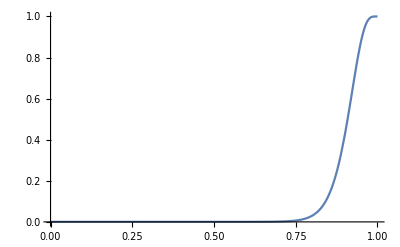

```mathematica
Plot[P2,{r,0,1}, PlotRange->{0, 1}]
```

```mathematica
r = .99
```

0.99

```mathematica
P2
```

0.999796

```mathematica
Clear[r]
```

```mathematica
H=2^8
```

256